```mathematica
Exit[]
```

```mathematica
$Assumptions=μ≥0&&σ>0&&a ∈ Reals&&1>k1≥0&&k0≥0&&S0>0&&K>0&&r≥0&&b ∈ Reals&& rf≥0&& γ>0;
u[W_]:=Exp[-γ W]
pr[B_]:=ⅇ^(-B^2/2)/√(2 π)
xx[B_]:=S0 Exp[ σ Sqrt[t] B+(μ-σ^2/2)t];
NIntegrate[xx[B]pr[B],{B,-∞,∞}]-S0
```

NIntegrate::inumr: The integrand ⅇ^-B^2/2 + B\ √t\ σ + t\ (μ - σ^2/2)\ S0/√2\ π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 0.}}.

-S0+NIntegrate[xx[B] pr[B],{B,-∞,∞}]

Short put

```mathematica
γ=.01;μ=0;t=1;k=550;S0=600;σ=.25;
put[W_]:=Max[0,k-W]
FinancialDerivative[{"European","Put"}, {"StrikePrice"-> k, "Expiration"->t},{"InterestRate"-> 0.0, "Volatility" -> σ, "CurrentPrice"-> S0, "Dividend"->0}]
p=NIntegrate[put[xx[B]]pr[B],{B,-∞,∞}]

q=Log[NIntegrate[u[-put[xx[B]]]pr[B],{B,-∞,∞}]]/γ
```

35.6083

35.6083

58.5032

Revision

```mathematica
γ=.01;k=550;S0=600;σSqrtT=.25;

p0=FinancialDerivative[{"European","Put"}, {"StrikePrice"-> k, "Expiration"->1},{"InterestRate"->0, "Volatility" -> σSqrtT, "CurrentPrice"-> S0}];

density[B_]:=ⅇ^(-B^2/2)/√(2 π)
put[B_]:=Max[0,k-S0 Exp[ σSqrtT B- σSqrtT^2/2]]
p1=NIntegrate[put[B]density[B],{B,-∞,∞}];
p2=1/γ Log[NIntegrate[Exp[γ put[B]]density[B],{B,-∞,∞}]];
{p0,p1,p2}
```

{35.6083,35.6083,58.5032}

Marginal utility-based price

```mathematica
μT=-0.08;
put[B_]:=Max[0,k-S0 Exp[ σSqrtT B+μT -σSqrtT^2/2]]
pP=NIntegrate[put[B]density[B],{B,-∞,∞}]

pP0=FinancialDerivative[{"European","Put"}, {"StrikePrice"-> k, "Expiration"->1},{"InterestRate"->0, "Dividend"-> -μT,"Volatility" -> σSqrtT, "CurrentPrice"-> S0}]
g[v_]:=-1/γ Log[NIntegrate[Exp[-γ v put[B]]density[B],{B,-∞,∞}]];
```

52.9911

52.9911

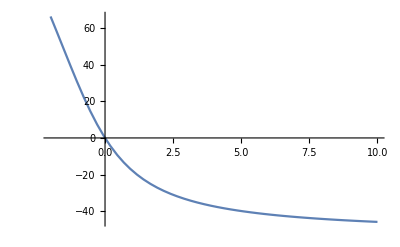

```mathematica
Plot[{g[v]/v-pP},{v,-2,10}]
```

Marginal utility-based price

```mathematica
μT=0;
put[B_]:=Max[0,k-S0 Exp[ σSqrtT B+μT -σSqrtT^2/2]]
pP=NIntegrate[put[B]density[B],{B,-∞,∞}]

pP0=FinancialDerivative[{"European","Put"}, {"StrikePrice"-> k, "Expiration"->1},{"InterestRate"->0, "Dividend"-> -μT,"Volatility" -> σSqrtT, "CurrentPrice"-> S0}]
g[v_,b_]:=1/γ Log[NIntegrate[Exp[-γ (b-v put[B])]density[B],{B,-∞,∞}]];
dg[v_,b_]:=NIntegrate[Exp[-γ (b-v put[B])](put[B]-b)density[B],{B,-∞,∞}];dg2[v_]:=NIntegrate[Exp[-γ (-v put[B])]put[B]density[B],{B,-∞,∞}];
{pR=g[1,0],dg2[1]/Exp[γ pR]}
v2=7;pR2=g[v2,0];{pR2/v2,dg2[v2]/Exp[γ pR2]}
```

35.6083

35.6083

{58.5032,87.9525}

{217.181,327.148}

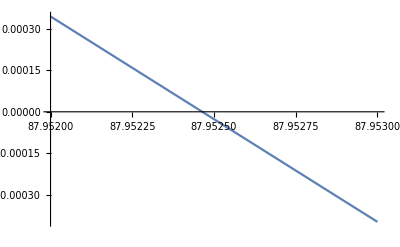

```mathematica
Plot[{dg[1,b]},{b,87.952,87.953}]
```

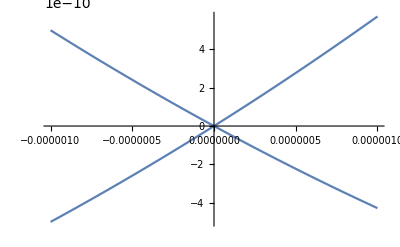

```mathematica
Plot[g[1-v,0]-pR+{v 87.952,v 87.953},{v,-0.000001,0.000001}]
```